```mathematica
Needs["Splines`"]
```

```mathematica
gap={2.54,2.64,2.74,2.84,2.94,3.04,3.14,3.24,3.34};
```

```mathematica
Tc={0.01564469490321565,0.016718486054705623,0.01790301697981826,0.018485095255092367,0.018993352326685663,0.019387116948092555,0.01918318794607454,0.018421543013126714,0.014501390741581306};
```

```mathematica
sgap={1.3180,1.3581,1.3987,1.4396,1.4809,1.5227,1.5648,1.6073,1.6502};
```

```mathematica
Tcabs=Table[Tc[[i]]/1.13*11606,{i,1,Length[NCu]}];
```

Part::partw: Part 10 of {0.0156447,0.0167185,0.017903,0.0184851,0.0189934,0.0193871,0.0191832,0.0184215,0.0145014} does not exist.

Part::partw: Part 11 of {0.0156447,0.0167185,0.017903,0.0184851,0.0189934,0.0193871,0.0191832,0.0184215,0.0145014} does not exist.

```mathematica
NCu={0.651039021 ,0.661724665 ,0.672300788 ,0.682720386 ,0.69289772 ,0.703112031 ,0.712965105 ,0.72276339 ,0.732167666 ,0.741535229 ,0.750384601};
```

```mathematica
Length[NCu]
```

11

```mathematica
Length[gap]
```

9

```mathematica
Eigenb50={0.89881,0.92755,0.94337,0.96846,0.98056,0.97923,0.98894,0.99040,0.98263,0.97062,0.97377};
Eigenb56={0.95223,0.96943,0.98775,1.01627,1.00411,1.01265,1.02021,1.00149,1.00768,0.99556,0.97960};
Eigenb64={0.98525,1.00014,1.00824,1.02406,1.01820,1.02281,1.02777,1.00827,0.99490,0.97982,0.97577};
```

```mathematica
NOx=Table[(1.15-NCu[[i]])/2,{i,1,Length[NCu]}];
```

```mathematica
Length[gap]
```

9

```mathematica
upperTicks=Module[{labels,positions},labels=Range[1.3,1.7,0.1];
positions=(2.374573135*#-0.578463015)&/@labels;
Transpose[{positions,labels}]];
```

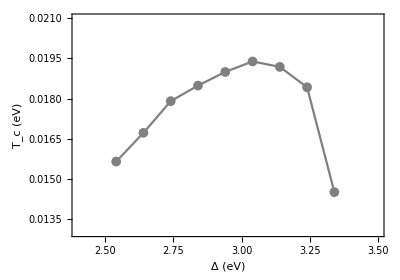

```mathematica
Tcvsdelta=ListPlot[Table[{gap[[i]],Tc[[i]]},{i,1,Length[NCu]-2}],BaseStyle->{FontSize->17.5,FontFamily->"times New Roman"},PlotRange->{{2.4,3.5},{0.013,0.021}},PlotMarkers->{Automatic,10},Frame->True,AspectRatio->0.7,FrameLabel->{{"T_c (eV)",None},{"Δ (eV)","Δ_s (eV)"}},PlotRange->{{0,0.08},All},PlotStyle->Gray,FrameTicks->{{Automatic,None},{Automatic,Join[upperTicks]}},Joined->True]
```

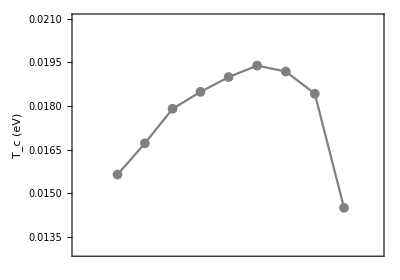

```mathematica
Tcvsgap=ListPlot[Table[{sgap[[i]],Tc[[i]]},{i,1,Length[NCu]-2}],BaseStyle->{FontSize->17.5,FontFamily->"times New Roman"},PlotRange->{{1.26,1.7},{0.013,0.021}},PlotMarkers->{Automatic,10},Frame->True,AspectRatio->0.7,FrameLabel->{{"T_c (eV)",None},{None,"Δ_s (eV)"}},FrameTicks->{Automatic,{None,upperTicks}},PlotRange->{{0,0.08},All},PlotStyle->Gray,Joined->True]
```

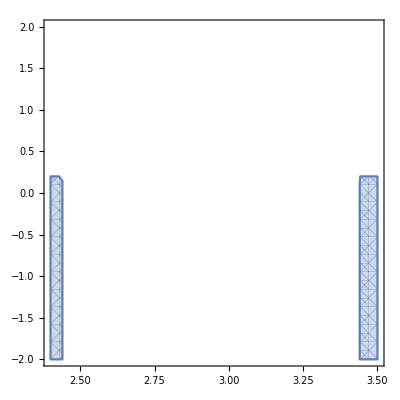

```mathematica
A=RegionPlot[(x<=2.44 || x≥3.44)&&y<0.2,{x,2.4,3.5},{y,-2,2}]
```

```mathematica
B=RegionPlot[x≥3.44,{x,2.4,2.6},{y,-2,2}];
```

```mathematica
fTcvsdelta=SplineFit[Table[{gap[[i]],Tc[[i]]},{i,1,9}],Cubic];
```

```mathematica
figTcvsdelta=ParametricPlot[Evaluate[Through[{fTcvsdelta}[t]]],{t,0,9},PlotStyle->Pink];
```

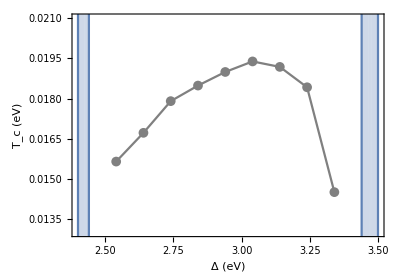

```mathematica
figTcvsdelta=Show[Tcvsdelta,(*figTcvsdelta,*)A(*,Graphics[Text[Style["(b)",FontSize->17.5,Black],{3.35,0.0205}]]*)]
```